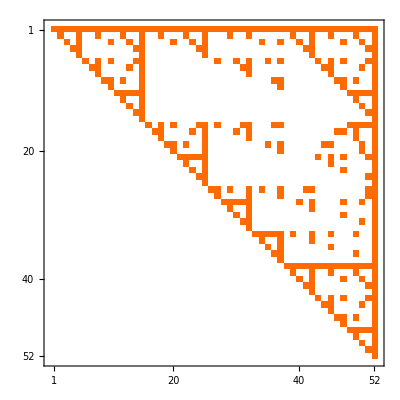

```mathematica
n13x2x4x5,n12x3x45,n1x235x4,n1x2x34x5,n1345x2,n1x235x4,n1x2345,n1x234x5,n1x2345,n1x2345,n1x235x4,n145x23,n1x235x4,n1x234x5,n1x2345,n15x23x4,n1345x2,n15x234,n1235x4,n15x234,n14x23x5,n1345x2,n14x235,n145x23,n12345,n145x23,n145x23,n13x2x4x5,n1345x2,n1235x4,n13x245,n13x245,n1235x4,n12345,n1345x2,n12345,n1345x2,n12x35x4,n12x3x45,n12x35x4,n12x345,n12x345,n1235x4,n125x34,n124x35,n12345,n12345,n1235x4,n12345,n1235x4,n12345,n12345
```

```mathematica
TopologicalSort[four]
```

{n12345,n1234x5,n1235x4,n123x45,n123x4x5,n1245x3,n124x35,n124x3x5,n125x34,n125x3x4,n12x345,n12x34x5,n12x35x4,n12x3x45,n12x3x4x5,n1345x2,n134x25,n134x2x5,n135x24,n135x2x4,n13x245,n13x24x5,n13x25x4,n13x2x45,n13x2x4x5,n145x23,n145x2x3,n14x235,n14x23x5,n14x25x3,n14x2x35,n14x2x3x5,n15x234,n15x23x4,n15x24x3,n15x2x34,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x45,n1x23x4x5,n1x245x3,n1x24x35,n1x24x3x5,n1x25x34,n1x25x3x4,n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45,n1x2x3x4x5}

```mathematica
DepthFirstScan
```

```mathematica
Table[Mob[k],{k,TopologicalSort[four]}]
```

{24,-6,-6,-2,2,-6,-2,2,-2,2,-2,1,1,1,-1,-6,-2,2,-2,2,-2,1,1,1,-1,-2,2,-2,1,1,1,-1,-2,1,1,1,-1,-6,2,2,1,-1,2,1,-1,1,-1,2,-1,-1,-1,1}

```mathematica
Table[Mob[k],{k,TopologicalSort[four]}]
```

{24,-6,-6,-2,2,-6,-2,2,-2,2,-2,1,1,1,-1,-6,-2,2,-2,2,-2,1,1,1,-1,-2,2,-2,1,1,1,-1,-2,1,1,1,-1,-6,2,2,1,-1,2,1,-1,1,-1,2,-1,-1,-1,1}

```mathematica
BreadthFirstScan[four]
```

{n13x2x45,n12x345,n1x2345,n1x2x345,n12345,n12345,n1x2345,n12345,n15x234,n12345,n12345,n14x235,n12345,n12345,n12345,n12x345,n12345,n12345,n12345,n12x3x45,n1x2x3x45,n12345,n123x45,n1x23x45,n12345,n1x2345,n12345,n13x245,n134x25,n12345,n13x245,n135x24,n13x245,n12345,n1x2345,n15x234,n124x35,n1x24x35,n1x2345,n14x2x35,n14x235,n145x23,n14x235,n125x34,n1x25x34,n1x2345,n15x2x34,n15x234,n12x345,n1x2345,n1x2x345,n1x2x345}

```mathematica
MyScan[g_,root_,visited_]:=Block[{result={},children,visited2=visited},

If[!MemberQ[visited2,root],
visited2 = Append[visited2,root];
children=Map[Last, Select[EdgeList[g],#[[1]]==root&]];
children=Sort[children,BaseVarComp2];
Table[
visited2=MyScan[g,child,visited2
]
,
{child,children}];
Print[children];
];
visited2
]
```

```mathematica
MyScan[four,n12345,{}]
```

{}

{n1x2x3x4x5}

{n1x2x3x4x5}

{n1x2x3x4x5}

{n12x3x4x5,n13x2x4x5,n1x23x4x5}

{n1x2x3x4x5}

{n1x2x3x4x5}

{n12x3x4x5,n14x2x3x5,n1x24x3x5}

{n1x2x3x4x5}

{n13x2x4x5,n14x2x3x5,n1x2x34x5}

{n1x23x4x5,n1x24x3x5,n1x2x34x5}

{n12x3x4x5,n1x2x34x5}

{n13x2x4x5,n1x24x3x5}

{n14x2x3x5,n1x23x4x5}

{n123x4x5,n124x3x5,n134x2x5,n1x234x5,n12x34x5,n13x24x5,n14x23x5}

{n1x2x3x4x5}

{n1x2x3x4x5}

{n12x3x4x5,n15x2x3x4,n1x25x3x4}

{n1x2x3x4x5}

{n13x2x4x5,n15x2x3x4,n1x2x35x4}

{n1x23x4x5,n1x25x3x4,n1x2x35x4}

{n12x3x4x5,n1x2x35x4}

{n13x2x4x5,n1x25x3x4}

{n15x2x3x4,n1x23x4x5}

{n123x4x5,n125x3x4,n135x2x4,n1x235x4,n12x35x4,n13x25x4,n15x23x4}

{n1x2x3x4x5}

{n14x2x3x5,n15x2x3x4,n1x2x3x45}

{n1x24x3x5,n1x25x3x4,n1x2x3x45}

{n12x3x4x5,n1x2x3x45}

{n14x2x3x5,n1x25x3x4}

{n15x2x3x4,n1x24x3x5}

{n124x3x5,n125x3x4,n145x2x3,n1x245x3,n12x3x45,n14x25x3,n15x24x3}

{n1x2x34x5,n1x2x35x4,n1x2x3x45}

{n13x2x4x5,n1x2x3x45}

{n14x2x3x5,n1x2x35x4}

{n15x2x3x4,n1x2x34x5}

{n134x2x5,n135x2x4,n145x2x3,n1x2x345,n13x2x45,n14x2x35,n15x2x34}

{n1x23x4x5,n1x2x3x45}

{n1x24x3x5,n1x2x35x4}

{n1x25x3x4,n1x2x34x5}

{n1x234x5,n1x235x4,n1x245x3,n1x2x345,n1x23x45,n1x24x35,n1x25x34}

{n123x4x5,n12x3x45,n13x2x45,n1x23x45}

{n124x3x5,n12x35x4,n14x2x35,n1x24x35}

{n125x3x4,n12x34x5,n15x2x34,n1x25x34}

{n1x2x345,n12x34x5,n12x35x4,n12x3x45}

{n134x2x5,n13x25x4,n14x25x3,n1x25x34}

{n135x2x4,n13x24x5,n15x24x3,n1x24x35}

{n1x245x3,n13x24x5,n13x25x4,n13x2x45}

{n145x2x3,n14x23x5,n15x23x4,n1x23x45}

{n1x235x4,n14x23x5,n14x25x3,n14x2x35}

{n1x234x5,n15x23x4,n15x24x3,n15x2x34}

{n1234x5,n1235x4,n1245x3,n1345x2,n1x2345,n123x45,n124x35,n125x34,n12x345,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234}

{n12345,n1234x5,n123x4x5,n12x3x4x5,n1x2x3x4x5,n13x2x4x5,n1x23x4x5,n124x3x5,n14x2x3x5,n1x24x3x5,n134x2x5,n1x2x34x5,n1x234x5,n12x34x5,n13x24x5,n14x23x5,n1235x4,n125x3x4,n15x2x3x4,n1x25x3x4,n135x2x4,n1x2x35x4,n1x235x4,n12x35x4,n13x25x4,n15x23x4,n1245x3,n145x2x3,n1x2x3x45,n1x245x3,n12x3x45,n14x25x3,n15x24x3,n1345x2,n1x2x345,n13x2x45,n14x2x35,n15x2x34,n1x2345,n1x23x45,n1x24x35,n1x25x34,n123x45,n124x35,n125x34,n12x345,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234}

```mathematica
MyScan[four,n12345,{}]
```

{n1x2345,n15x234,n14x235,n145x23,n13x245,n135x24,n134x25,n1345x2,n12x345,n125x34,n124x35,n1245x3,n123x45,n1235x4,n1234x5}

```mathematica
Length[{n12345,n1234x5,n123x4x5,n12x3x4x5,n1x2x3x4x5,n13x2x4x5,n1x23x4x5,n124x3x5,n14x2x3x5,n1x24x3x5,n134x2x5,n1x2x34x5,n1x234x5,n12x34x5,n13x24x5,n14x23x5,n1235x4,n125x3x4,n15x2x3x4,n1x25x3x4,n135x2x4,n1x2x35x4,n1x235x4,n12x35x4,n13x25x4,n15x23x4,n1245x3,n145x2x3,n1x2x3x45,n1x245x3,n12x3x45,n14x25x3,n15x24x3,n1345x2,n1x2x345,n13x2x45,n14x2x35,n15x2x34,n1x2345,n1x23x45,n1x24x35,n1x25x34,n123x45,n124x35,n125x34,n12x345,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234}]
```

52